```mathematica
sols=Solve[{dx/Δt==-v,v==v0(1-dx/Δx)+v1 dx/Δx},{dx,v}]//FullSimplify
```

{{dx→(v0 Δt Δx)/(v0 Δt-v1 Δt-Δx),v→-(v0 Δx)/(v0 Δt-v1 Δt-Δx)}}

```mathematica
dxsol=sols[[1]][[1]][[2]]
vsol=sols[[1]][[2]][[2]]
dxnum=sols[[1]][[1]][[2]]/.{Δx->761,Δt->10,v1->-16.16};
vnum=sols[[1]][[2]][[2]]/.{Δx->761,Δt->1,v1->-16.16};
```

(v0 Δt Δx)/(v0 Δt-v1 Δt-Δx)

-(v0 Δx)/(v0 Δt-v1 Δt-Δx)

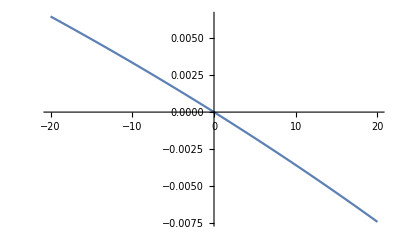

```mathematica
Plot[dxnum,{v0,-20,20}]
```

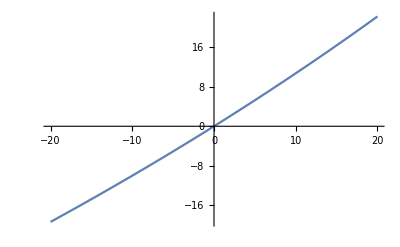

```mathematica
Plot[vnum,{v0,-20,20}]
```

```mathematica
v0crit=Solve[0==1/vsol,v0]//Simplify
```

{{v0→v1+Δx/Δt}}

```mathematica
(dxsol/Δx)/.{Δx->0.526316,Δt->0.000691386,v1->-16.1597,v0->-12.1089}
```

0.0159917